# HyperBloch package tutorial

## Supercells

This notebook provides solved exercises aimed to introduce the functionality of the  HyperBloch package for efficient modeling of tight-binding models on hyperbolic lattices. It is intended to be used in tandem with the HyperBloch Supercells tutorial on the HyperCells&HyperBloch website. In this tutorial the import of supercell model graphs (constructed through HyperBloch’s sister package HyperCells) and the construction of corresponding Abelian Bloch Hamiltonians  is showcased, which is supplemented by a demonstration of the  supercell method through density of states calculations.

## Preliminaries:

### Remarks:

Before using the notebook to the supercells tutorial:

Make sure that the HyperBloch package is installed, if this is not the case please follow the instruction on the website HyperCells&HyperBloch installation.

Make sure that the required files .hcm and .hcs files are in the current directory. This entails the files:

{8,8}-tess_< PC >_ 3.hcm
  {8,8}-tess_< PC >_ 3_sc-< SC >.hcs 
   where < PC > is a placeholder for the primitive cells and < SC > is a place holder for the supercells:
   
   #Supercell sequence  |   < PC >    |	< SC >
   -----------------------------------------------------------------------------------------------------------
    1.				       |   T2.6	       |   {T3 .11, T5 .13, T9 .20, T17 .29, T33 .44, T65 .78}
    1A.			       |   T3.10     |	 {T5.13, T9.22, T17.35, T33.58, T65.81}
    2A.			       |   T5.12     |	 {T9.22, T17.32, T33.46, T65.79}

In case no such files exist in your current directory, please follow the instructions in the prerequisites section of the HyperBloch Supercells tutorial, or download it there.

### Documentation:

You may want to take a look at the basic usage guide of the HyperBloch package or the available functions within the package, respectively:

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/tutorial/BasicUsage"];
```

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/guide/HyperBlochPackage"];
```

### Load the HyperBloch package:

The HyperBloch package can be loaded as follows:

```mathematica
<<PatrickMLenggenhager`HyperBloch`
```

Set the directory of the needed HyperCells files remarked above, which is assumed to be the directory of this file:

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Supercell sequence 1:

### Preliminaries:

We consider the following sequence of supercells, defined in terms of triangle group quotients given in the tabulated list of quotients by Marston Conder:

```mathematica
cells={"T2.6","T3.11","T5.13","T9.20","T17.29","T33.44","T65.78"};
```

where we consider the unit cell T2.6 as the primitive cell.

### Import (supercell) model graphs:

We first import the model, and supercell model graphs as produced by the HyperCells package:

Primitive cell:

```mathematica
pcmodel=ImportModelGraphString[Import["{8,8}-tess_T2.6_3.hcm"]];
```

Consecutive supercells:

```mathematica
scmodels=Association[#->ImportSupercellModelGraphString[ Import["{8,8}-tess_T2.6_3_sc-"<>#<>".hcs"]]&/@cells[[2;;]]];
```

We can extract the genera of the compactified unit cells programmatically:

```mathematica
genusLst = Join[
Association[cells[[1]]->pcmodel["Genus"]],
Association[#->scmodels[#]["Genus"]&/@cells[[2;;]]]
];
```

### Construct Abelian Bloch Hamiltonians:

Once the (supercell) model graphs are imported the corresponding Abelian Bloch Hamiltonians can be constructed.

Primitive cell:

```mathematica
Hpc=AbelianBlochHamiltonian[pcmodel,1,0&,-1&,CompileFunction->True];
```

Consecutive supercells (this might take a minute):

```mathematica
Hsclst=Association[#->AbelianBlochHamiltonian[scmodels[#],1,0&,-1&,PCModel->pcmodel,CompileFunction->True]&/@cells[[2;;]]];
```

For convenience, let us collect the constructed Hamiltonians in one Association:

```mathematica
Hclst=Join[Association[cells[[1]]->Hpc],Hsclst];
```

### Eigenvalues:

In order to proceed we define the following function which enables us compute the density of states by exact diagonalization. We can take advantage of the independence of different momentum sectors and therefore parallelize it, where we partition the set of Npts into  Nruns subsets:

```mathematica
ComputeEigenvalues[cfH_,Npts_,Nruns_,genus_]:=
Flatten@ParallelTable[
Flatten@Table[
Eigenvalues[cfH@@RandomReal[{-Pi,Pi},2genus]],
{i,1,Round[Npts/Nruns]}],
{j,1,Nruns},
Method->"FinestGrained"]
```

### Density of states:

We compute the Eigenvalues with a set of  5·10^4 random samples in momentum space and 32 subsets, (this might take a minute):

```mathematica
evals=Association[#->ComputeEigenvalues[Hclst[#], 5 10^4,32,genusLst[#]]&/@cells];
```

Let us construct a list of colors for the different unit cells we are considering:

```mathematica
cLst=(ColorData["SunsetColors","ColorFunction"]/@(1-Range[1,7]/7.));
```

We choose to visualize the density of states via a kernel density estimation with an energy binwidth of 0.05, (this might take a minute):

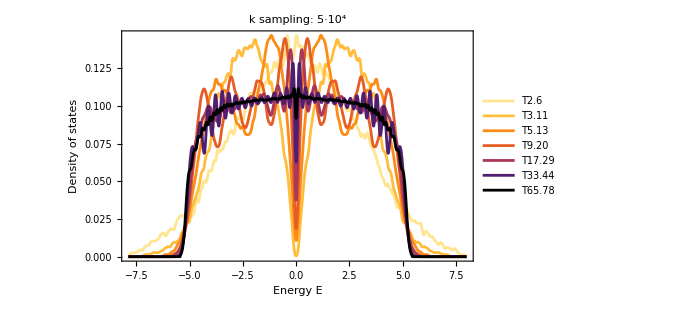

```mathematica
SmoothHistogram[evals,0.05,"PDF",
Frame->True,FrameLabel->{"Energy E","Density of states"},FrameStyle->Black,
ImageSize->500,ImagePadding->{{Automatic, 10}, {Automatic, 10}},LabelStyle->20,
PlotLabel->"k sampling: 5·10^4",PlotRange->All, PlotStyle->cLst]
```

## Supercell sequence 1A:

### Preliminaries:

We may also consider various other sequences of supercells for the application of the supercell method. As we have done before, we consider the next supercell sequence in terms of triangle group quotients given in the tabulated list of quotients by Marston Conder:

```mathematica
cells={"T3.10","T5.13","T9.22","T17.35","T33.58","T65.81"};
```

where we consider the unit cell T3.10 as the primitive cell.

### Import (supercell) model graphs:

We first import the model, and supercell model graphs as produced by the HyperCells package:

Primitive cell:

```mathematica
pcmodel=ImportModelGraphString[Import["{8,8}-tess_T3.10_3.hcm"]];
```

Consecutive supercells:

```mathematica
scmodels=Association[#->ImportSupercellModelGraphString[ Import["{8,8}-tess_T3.10_3_sc-"<>#<>".hcs"]]&/@cells[[2;;]]];
```

We can extract the genera of the compactified unit cells programmatically:

```mathematica
genusLst = Join[
Association[cells[[1]]->pcmodel["Genus"]],
Association[#->scmodels[#]["Genus"]&/@cells[[2;;]]]
];
```

### Construct Abelian Bloch Hamiltonians:

Once the (supercell) model graphs are imported the corresponding Abelian Bloch Hamiltonians can be constructed.

Primitive cell:

```mathematica
Hpc=AbelianBlochHamiltonian[pcmodel,1,0&,-1&,CompileFunction->True];
```

Consecutive supercells (this might take a minute):

```mathematica
Hsclst=Association[#->AbelianBlochHamiltonian[scmodels[#],1,0&,-1&,PCModel->pcmodel,CompileFunction->True]&/@cells[[2;;]]];
```

For convenience, let us collect the constructed Hamiltonians in one Association:

```mathematica
Hclst=Join[Association[cells[[1]]->Hpc],Hsclst];
```

### Density of states:

We compute the Eigenvalues with a set of  5·10^4 random samples in momentum space and 32 subsets, (this might take a minute):

```mathematica
evals=Association[#->ComputeEigenvalues[Hclst[#], 5 10^4,32,genusLst[#]]&/@cells];
```

Let us construct a list of colors for the different unit cells we are considering:

```mathematica
cLst=(ColorData["SunsetColors","ColorFunction"]/@(1-Range[1,6]/6.));
```

We choose to visualize the density of states via a kernel density estimation with an energy binwidth of 0.05, (this might take a minute):

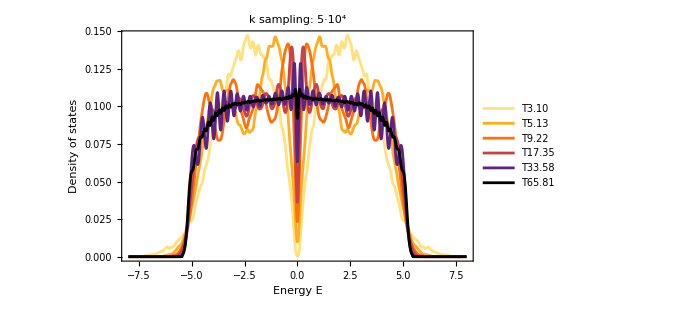

```mathematica
SmoothHistogram[evals,0.05,"PDF",
Frame->True,FrameLabel->{"Energy E","Density of states"},FrameStyle->Black,
ImageSize->500,ImagePadding->{{Automatic, 10}, {Automatic, 10}},LabelStyle->20,
PlotLabel->"k sampling: 5·10^4",PlotRange->{{-8,8},Automatic},PlotStyle->cLst]
```

## Supercell sequence 2A:

### Preliminaries:

Let us consider yet another supercell sequence. As we have done before, we consider the next supercell sequence in terms of triangle group quotients given in the tabulated list of quotients by Marston Conder:

```mathematica
cells={"T5.12","T9.22","T17.32","T33.46","T65.79"};
```

where we consider the unit cell T5.12 as the primitive cell.

### Import (supercell) model graphs:

We first import the model, and supercell model graphs as produced by the HyperCells package:

Primitive cell:

```mathematica
pcmodel=ImportModelGraphString[Import["{8,8}-tess_T5.12_3.hcm"]];
```

Consecutive supercells:

```mathematica
scmodels=Association[#->ImportSupercellModelGraphString[ Import["{8,8}-tess_T5.12_3_sc-"<>#<>".hcs"]]&/@cells[[2;;]]];
```

We can extract the genera of the compactified unit cells programmatically:

```mathematica
genusLst = Join[
Association[cells[[1]]->pcmodel["Genus"]],
Association[#->scmodels[#]["Genus"]&/@cells[[2;;]]]
];
```

### Construct Abelian Bloch Hamiltonians:

Once the (supercell) model graphs are imported the corresponding Abelian Bloch Hamiltonians can be constructed.

Primitive cell:

```mathematica
Hpc=AbelianBlochHamiltonian[pcmodel,1,0&,-1&,CompileFunction->True];
```

Consecutive supercells (this might take a minute):

```mathematica
Hsclst=Association[#->AbelianBlochHamiltonian[scmodels[#],1,0&,-1&,PCModel->pcmodel,CompileFunction->True]&/@cells[[2;;]]];
```

For convenience, let us collect the constructed Hamiltonians in one Association:

```mathematica
Hclst=Join[Association[cells[[1]]->Hpc],Hsclst];
```

### Density of states:

We compute the Eigenvalues with a set of  5·10^4 random samples in momentum space and 32 subsets, (this might take a minute):

```mathematica
evals=Association[#->ComputeEigenvalues[Hclst[#], 5 10^4,32,genusLst[#]]&/@cells];
```

Let us construct a list of colors for the different unit cells we are considering:

```mathematica
cLst=(ColorData["SunsetColors","ColorFunction"]/@(1-Range[1,5]/5.));
```

We choose to visualize the density of states via a kernel density estimation with an energy binwidth of 0.05, (this might take a minute):

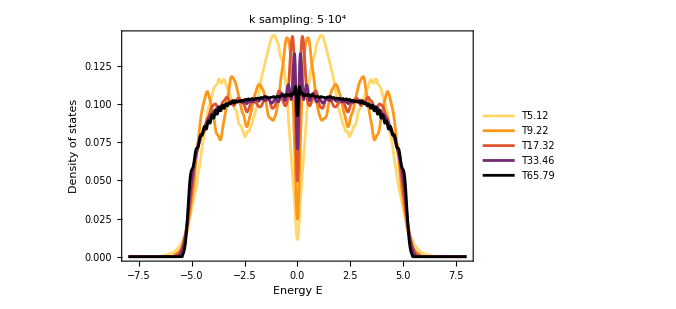

```mathematica
SmoothHistogram[evals,0.05,"PDF",
Frame->True,FrameLabel->{"Energy E","Density of states"},FrameStyle->Black,
ImageSize->500,ImagePadding->{{Automatic, 10}, {Automatic, 10}},LabelStyle->20,
PlotLabel->"k sampling: 5·10^4",PlotRange->{{-8,8},Automatic}, PlotStyle->cLst]
```

```mathematica
NotebookSave[]
```